```mathematica
MaxLLpar={a->0.27,β->2.,ϵ->0.106,η->0.0061,t0->80.,η0->0.49, κ-> 2.1, Xcrit->10,Yc->2}
```

{a→0.27,β→2.,ϵ→0.106,η→0.0061,t0→80.,η0→0.49,κ→2.1,Xcrit→10,Yc→2}

Potential function and steady state:

```mathematica
UUy[Y_, t_]=Integrate[-η t+β ⅇ^(a Y)/(ⅇ^(a κ)+ⅇ^(a Y)),Y]
```

-t Y η+(β Log[ⅇ^(a Y)+ⅇ^(a κ)])/a

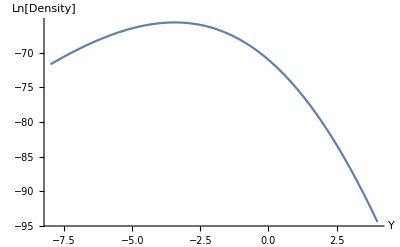

```mathematica
Plot[(-UUy[Y, t]/ϵ)/.{t->60}/.MaxLLpar,{Y,-8,4},AxesLabel->{"Y","Ln[Density]"}]
```

Distribution of damage Level:

```mathematica
BoltzmannFactor[Y_,t_]=Exp[-UUy[Y, t]/ϵ]//FullSimplify
```

ⅇ^((t Y η-(β Log[ⅇ^(a Y)+ⅇ^(a κ)])/a)/ϵ)

```mathematica
BoltzmannFactorIntegral[Y_, t_]=Integrate[Exp[t Y η/ϵ-(β Log[ⅇ^(a Y)+ⅇ^(a κ)])/(a ϵ)],Y]//FullSimplify
```

(ⅇ^((t Y η)/ϵ-a κ) (ⅇ^(a Y)+ⅇ^(a κ))^(1-β/(a ϵ)) ϵ Hypergeometric2F1[1,(-β+a ϵ+t η)/(a ϵ),1+(t η)/(a ϵ),-ⅇ^(a (Y-κ))])/(t η)

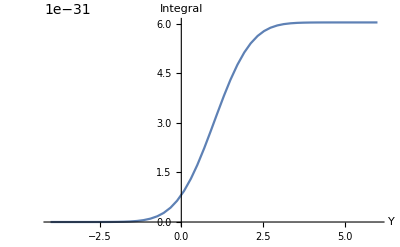

```mathematica
Plot[BoltzmannFactorIntegral[Y, t]/.{t->60+t0}/.MaxLLpar,{Y,-4,6},AxesLabel->{"Y","Integral"}]
```

```mathematica
fx[X_, t_]=BoltzmannFactor[Log@X, t]/X//FullSimplify
```

X^(-1+(t η)/ϵ) (ⅇ^(a κ)+X^a)^(-β/(a ϵ))

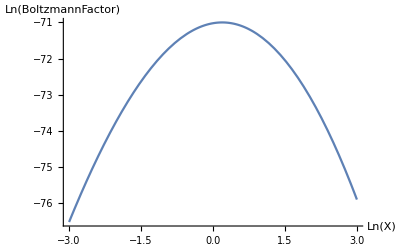

```mathematica
Plot[(Log@fx[Exp@Y,t])/.{t->60+t0}/.MaxLLpar,{Y,-3,3},AxesLabel->{"Ln(X)","Ln(BoltzmannFactor)"}]
```

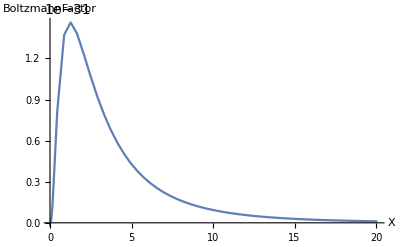

```mathematica
Plot[fx[X,t]/.{t->60+t0}/.MaxLLpar,{X,Exp@-3,Exp@3},AxesLabel->{"X","BoltzmannFactor"},PlotRange->Full]
```

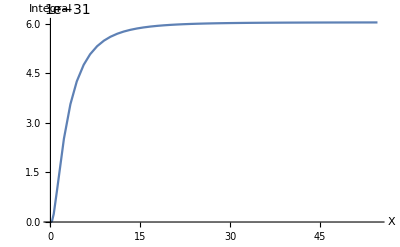

```mathematica
Plot[NIntegrate[fx[X,t]/.{t->60+t0}/.MaxLLpar,{X,Exp@-4,Xup}],{Xup,Exp@-4,Exp@4},AxesLabel->{"X","Integral"},PlotRange->Full]
```

```mathematica
NIntegrate[fx[X,t]/.{t->60+t0}/.MaxLLpar,{X,0.001,50}]
```

6.03627×10^-31

```mathematica
BoltzmannFactorIntegral[Y, t]/.{t->60+t0}/.MaxLLpar/.{Y->Log@50}
```

6.03627×10^-31

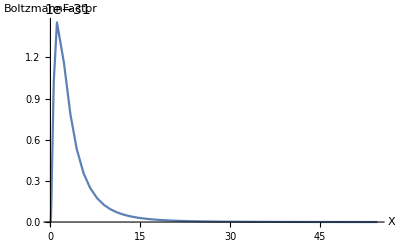

```mathematica
Plot[fx[X,t]/.{t->60+t0}/.MaxLLpar,{X,Exp@-4,Exp@4},AxesLabel->{"X","BoltzmannFactor"},PlotRange->Full]
```

```mathematica
DamageMean[age_,par_,Xmax_]:=NIntegrate[X*fx[X,t]/.{t->age+t0}/.par,{X,0.001,Xmax}]/(BoltzmannFactorIntegral[Y, t]/.{t->age+t0}/.par/.{Y->Log@Xmax})
```

```mathematica
DamageMean[age_,par_,Xmax_]:=NIntegrate[X*fx[X,t]/.{t->age+t0}/.par,{X,0.001,Xmax}]/NIntegrate[fx[X,t]/.{t->age+t0}/.par,{X,0.001,Xmax}]
```

```mathematica
DamageStd[age_,par_,Xmax_]:=Sqrt@(NIntegrate[X*X*fx[X,t]/.{t->age+t0}/.par,{X,0.001,Xmax}]/(BoltzmannFactorIntegral[Y, t]/.{t->age+t0}/.par/.{Y->Log@Xmax})-DamageMean[age, par,Xmax]^2)
```

```mathematica
DamageStd[age_,par_,Xmax_]:=Sqrt@(NIntegrate[X*X*fx[X,t]/.{t->age+t0}/.par,{X,0.001,Xmax}]/NIntegrate[fx[X,t]/.{t->age+t0}/.par,{X,0.001,Xmax}]-DamageMean[age, par,Xmax]^2)
```

```mathematica
DamageCV[age_,par_,Xmax_]:=Sqrt@(NIntegrate[X^2*fx[X,t]/.{t->age+t0}/.par,{X,0.001,Xmax}]/(BoltzmannFactorIntegral[Y, t]/.{t->age+t0}/.par/.{Y->Log@Xmax})*DamageMean[age, par,Xmax]^-2-1)
```

```mathematica
DamageCV[age_,par_,Xmax_]:=DamageStd[age, par,Xmax]/DamageMean[age, par,Xmax]
```

```mathematica
DamageSkew[age_,par_,Xmax_]:=DamageStd[age, par,Xmax]^-3(NIntegrate[X*X*X*fx[X,t]/.{t->age+t0}/.par,{X,0.001,Xmax}]/(BoltzmannFactorIntegral[Y, t]/.{t->age+t0}/.par/.{Y->Log@Xmax})-3DamageMean[age, par,Xmax] DamageStd[age, par,Xmax]^2-DamageMean[age, par,Xmax]^3)
```

```mathematica
DamageSkew[age_,par_,Xmax_]:=DamageStd[age, par,Xmax]^-3(NIntegrate[X*X*X*fx[X,t]/.{t->age+t0}/.par,{X,0.001,Xmax}]/(NIntegrate[fx[X,t]/.{t->age+t0}/.par,{X,0.001,Xmax}])-3DamageMean[age, par,Xmax] DamageStd[age, par,Xmax]^2-DamageMean[age, par,Xmax]^3)
```

```mathematica
Upp[Y_,t_]=D[UUy[Y,t],{Y,2}]
```

((-(a^2 ⅇ^(2 a Y))/((ⅇ^(a Y)+ⅇ^(a κ))^2)+(a^2 ⅇ^(a Y))/(ⅇ^(a Y)+ⅇ^(a κ))) β)/a

```mathematica
SSy[t]=Log[(ⅇ^(a κ) t η)/(β-t η)]/a
```

Log[(ⅇ^(a κ) t η)/(β-t η)]/a

```mathematica
h[t_]=Exp[(UUy[0,t]-UUy[Yc,t])/ϵ]/2/Pi*Sqrt[Upp[ Yc,t]*Upp[0,t]]//FullSimplify
```

(ⅇ^((t Yc η)/ϵ) (1+ⅇ^(a κ))^(β/(a ϵ)) (ⅇ^(a Yc)+ⅇ^(a κ))^(-β/(a ϵ)) √((a^2 ⅇ^(a (Yc+2 κ)) β^2)/((1+ⅇ^(a κ))^2 (ⅇ^(a Yc)+ⅇ^(a κ))^2)))/(2 π)

```mathematica
hss[t_]=Exp[(UUy[SSy[t],t]-UUy[Yc,t])/ϵ]/2/Pi*Sqrt[Upp[Yc,t]*Upp[SSy[t],t]]//FullSimplify
```

(ⅇ^((t Yc η)/ϵ) (ⅇ^(a Yc)+ⅇ^(a κ))^(-β/(a ϵ)) ((ⅇ^(a κ) β)/(β-t η))^(β/(a ϵ)) ((ⅇ^(a κ) t η)/(β-t η))^(-(t η)/(a ϵ)) √(-(a^2 ⅇ^(a (Yc+κ)) t η (-β+t η))/((ⅇ^(a Yc)+ⅇ^(a κ))^2)))/(2 π)

```mathematica
CumulativeHazard[T_]:=NIntegrate[hss[t]/.{t->age+t0}/.higherEta,{age,0,T}];
Survivorship[T_]:=Exp[-NIntegrate[hss[t]/.{t->age+t0}/.higherEta,{age,0,T}]]
```

```mathematica
linearTicks={Charting`ScaledTicks[{Identity,Identity},TicksLength->{.03,0.}][##,{5,1}]&,Charting`ScaledTicks[{Identity,Identity},TicksLength->{.03,0.}][##,{4,1}]&};
```

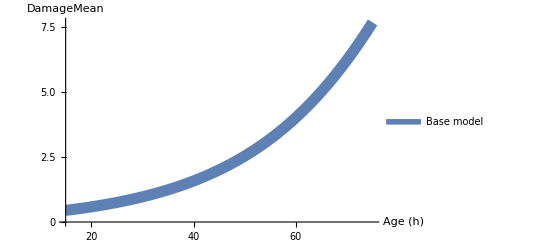
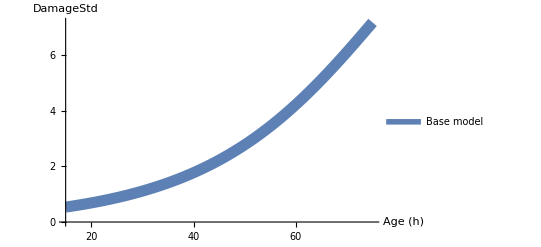
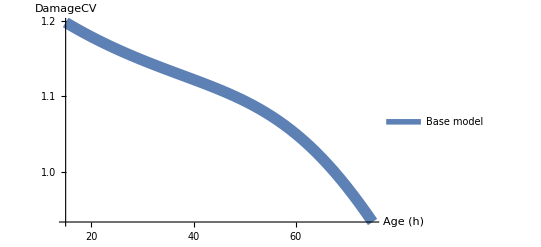
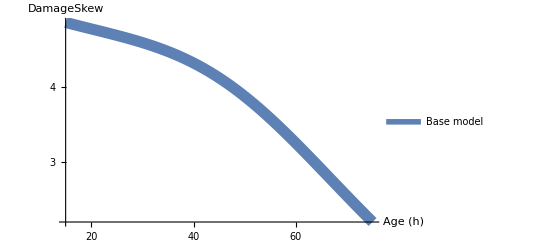
<|DamageMean→-Graphics-,DamageStd→-Graphics-,DamageCV→-Graphics-,DamageSkew→-Graphics-|>

```mathematica
Xmax=50;
momentsPlots=Association[Table[ToString[func]->Plot[Legended[func[age, MaxLLpar,Xmax],"Base model"],{age,15,75},AxesLabel->{"Age (h)",func},PlotStyle->Thickness[.02], Ticks->linearTicks,AxesStyle->Directive[Thickness[.01],Black]],{func,{DamageMean,DamageStd,DamageCV,DamageSkew}}]]
```

```mathematica
BetaEffect=.6;EtaEffect=.6;
lowerBeta=MaxLLpar; lowerBeta[[2, 2]] = MaxLLpar[[2, 2]]*(1-BetaEffect);
higherEta=MaxLLpar; higherEta[[4, 2]] = MaxLLpar[[4, 2]]*(1+EtaEffect);
higherEtalowerBeta=MaxLLpar; higherEtalowerBeta[[4, 2]] = MaxLLpar[[4, 2]]*(1+EtaEffect/2);higherEtalowerBeta[[2, 2]] = MaxLLpar[[2, 2]]*(1-BetaEffect/2);
lowerBetalowerEps=MaxLLpar; lowerBetalowerEps[[2, 2]] = MaxLLpar[[2, 2]]/(1+EtaEffect);lowerBetalowerEps[[3, 2]] = MaxLLpar[[3, 2]]/(1+EtaEffect);
```

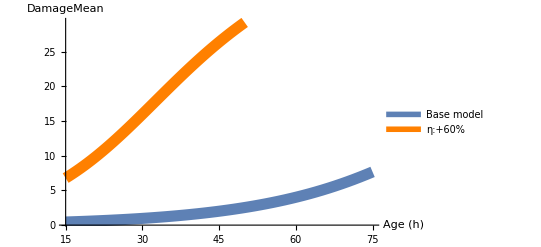
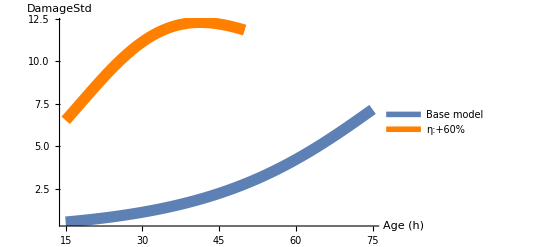
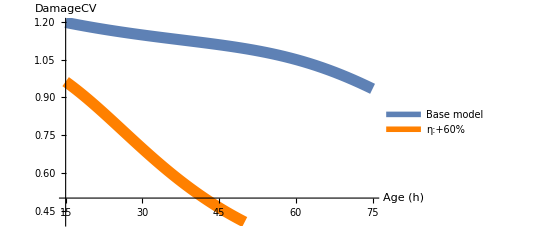
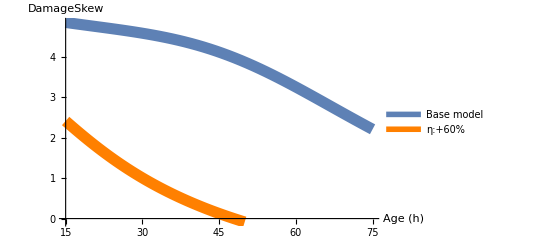
<|DamageMean→-Graphics-,DamageStd→-Graphics-,DamageCV→-Graphics-,DamageSkew→-Graphics-|>

```mathematica
momentsPlotsEta=Association[Table[ToString[func]->Show[momentsPlots[[ToString[func]]],Plot[Legended[func[age, higherEta,Xmax],"η:+60%"],{age,15,50},AxesLabel->{"Age (h)",func},PlotStyle->Directive[Thickness[.02],Orange]],PlotRange->All,Ticks->linearTicks,AxesStyle->Directive[Thickness[.01],Black],AxesOrigin->If[ToString[func]=="DamageCV",{15,0.5},{15,0.}]],{func,{DamageMean,DamageStd,DamageCV,DamageSkew}}]]
```

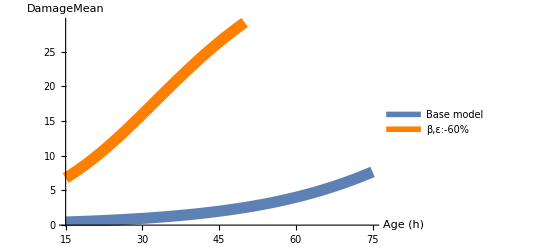
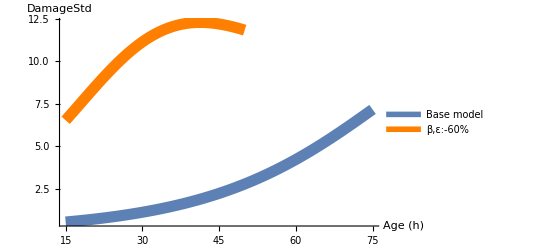
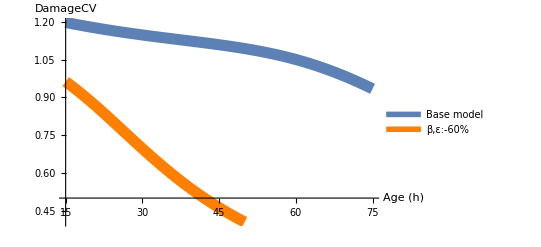
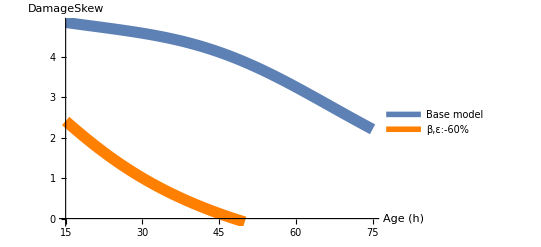
<|DamageMean→-Graphics-,DamageStd→-Graphics-,DamageCV→-Graphics-,DamageSkew→-Graphics-|>

```mathematica
momentsPlotsBetaEps=Association[Table[ToString[func]->Show[momentsPlots[[ToString[func]]],Plot[Legended[func[age, lowerBetalowerEps,Xmax],"β,ε:-60%"],{age,15,50},AxesLabel->{"Age (h)",func},PlotStyle->Directive[Thickness[.02],Orange]],PlotRange->All,Ticks->linearTicks,AxesStyle->Directive[Thickness[.01],Black],AxesOrigin->If[ToString[func]=="DamageCV",{15,0.5},{15,0.}]],{func,{DamageMean,DamageStd,DamageCV,DamageSkew}}]]
```

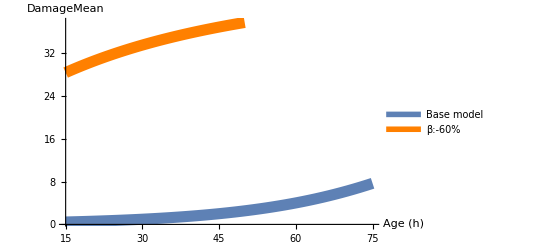
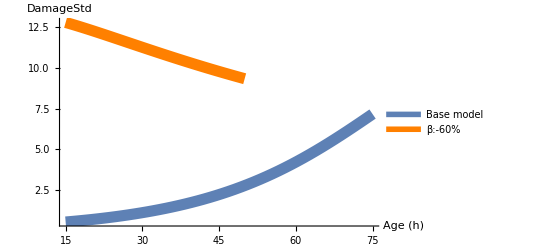
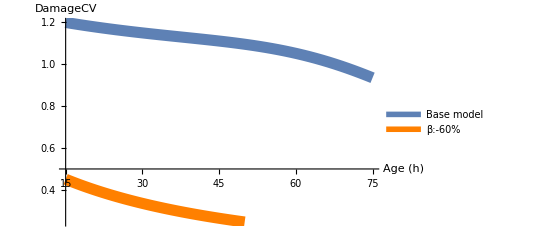
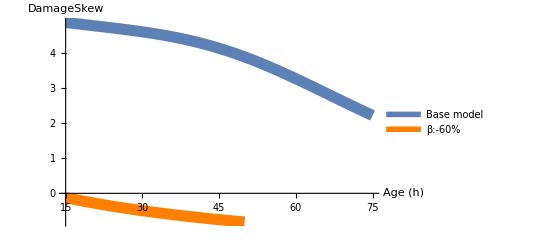
<|DamageMean→-Graphics-,DamageStd→-Graphics-,DamageCV→-Graphics-,DamageSkew→-Graphics-|>

```mathematica
momentsPlotsBeta=Association[Table[ToString[func]->Show[momentsPlots[[ToString[func]]],Plot[Legended[func[age, lowerBeta,Xmax],"β:-60%"],{age,15,50},AxesLabel->{"Age (h)",func},PlotStyle->Directive[Thickness[.02],Orange]],PlotRange->All,Ticks->linearTicks,AxesStyle->Directive[Thickness[.01],Black],AxesOrigin->If[ToString[func]=="DamageCV",{15,0.5},{15,0.}]],{func,{DamageMean,DamageStd,DamageCV,DamageSkew}}]]
```

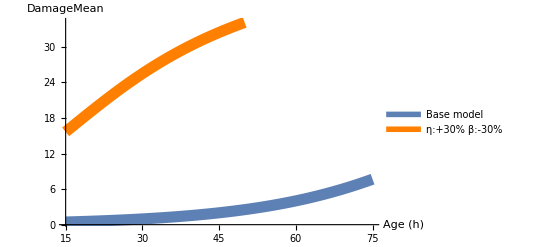
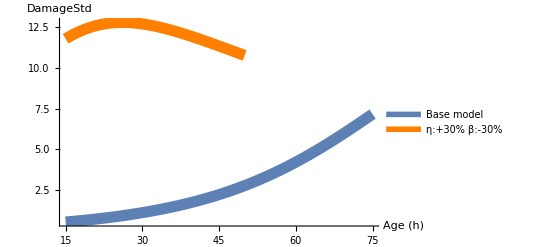
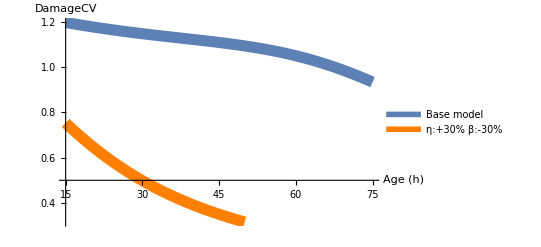
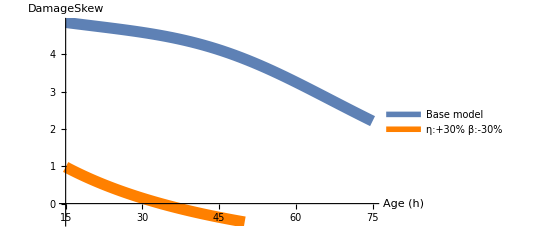
<|DamageMean→-Graphics-,DamageStd→-Graphics-,DamageCV→-Graphics-,DamageSkew→-Graphics-|>

```mathematica
momentsPlotsEtaBeta=Association[Table[ToString[func]->Show[momentsPlots[[ToString[func]]],Plot[Legended[func[age, higherEtalowerBeta,Xmax],"η:+30% β:-30%"],{age,15,50},AxesLabel->{"Age (h)",func},PlotStyle->Directive[Thickness[.02],Orange]],PlotRange->All,Ticks->linearTicks,AxesStyle->Directive[Thickness[.01],Black],AxesOrigin->If[ToString[func]=="DamageCV",{15,0.5},{15,0.}]],{func,{DamageMean,DamageStd,DamageCV,DamageSkew}}]]
```

```mathematica
EpsEffect=1.;AEffect=.5;
higherEps=MaxLLpar; higherEps[[3, 2]] = MaxLLpar[[3, 2]]*(1+EpsEffect);
higherA=MaxLLpar; higherA[[1, 2]] = higherA[[1, 2]]*(1+AEffect);
```

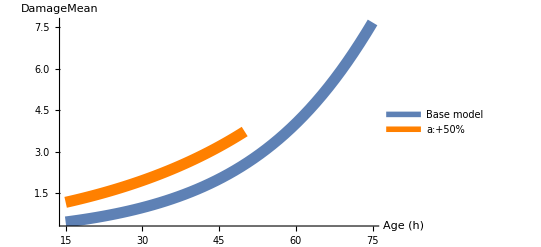
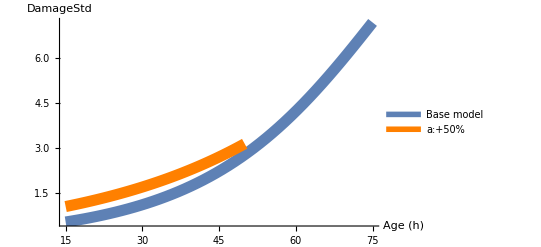
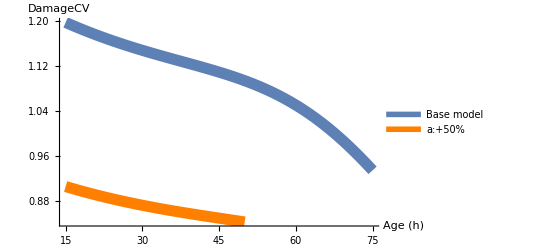
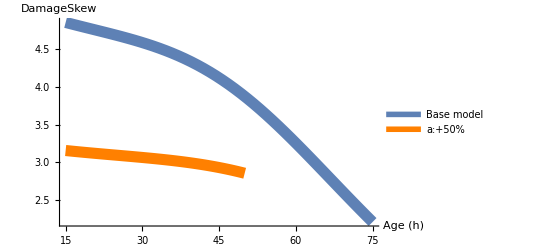
<|DamageMean→-Graphics-,DamageStd→-Graphics-,DamageCV→-Graphics-,DamageSkew→-Graphics-|>

```mathematica
momentsPlotsKappa=Association[Table[ToString[func]->Show[momentsPlots[[ToString[func]]],Plot[Legended[func[age, higherA,Xmax],"a:+50%"],{age,15,50},AxesLabel->{"Age (h)",func},PlotStyle->Directive[Thickness[.02],Orange]],PlotRange->All,Ticks->linearTicks,AxesStyle->Directive[Thickness[.01],Black],AxesOrigin->If[ToString[func]=="DamageCV",{15,0.5},{15,0.}]],{func,{DamageMean,DamageStd,DamageCV,DamageSkew}}]]
```

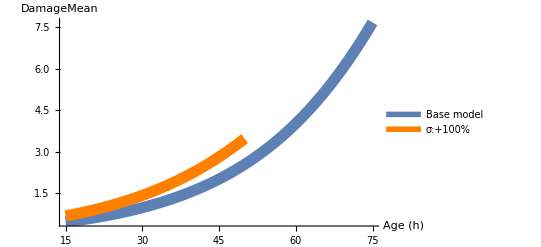
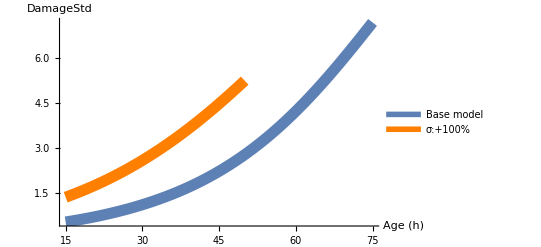
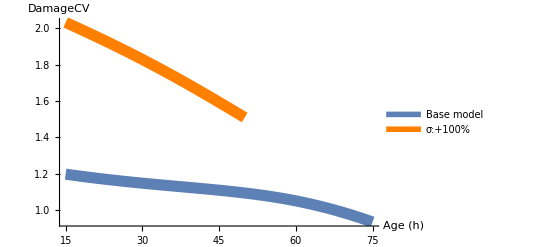
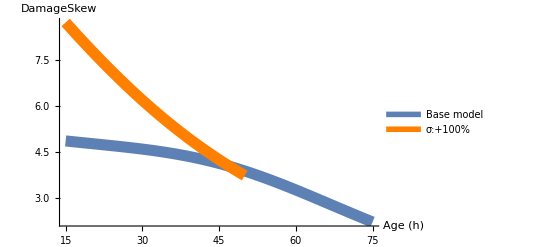
<|DamageMean→-Graphics-,DamageStd→-Graphics-,DamageCV→-Graphics-,DamageSkew→-Graphics-|>

```mathematica
momentsPlotsEps=Association[Table[ToString[func]->Show[momentsPlots[[ToString[func]]],Plot[Legended[func[age, higherEps,Xmax],"σ:+100%"],{age,15,50},AxesLabel->{"Age (h)",func},PlotStyle->Directive[Thickness[.02],Orange]],PlotRange->All,Ticks->linearTicks,AxesStyle->Directive[Thickness[.01],Black],AxesOrigin->If[ToString[func]=="DamageCV",{15,0.5},{15,0.}]],{func,{DamageMean,DamageStd,DamageCV,DamageSkew}}]]
```

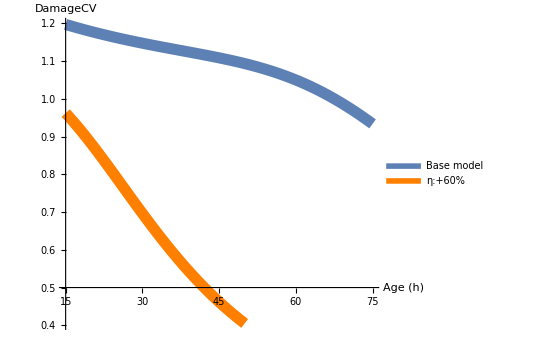
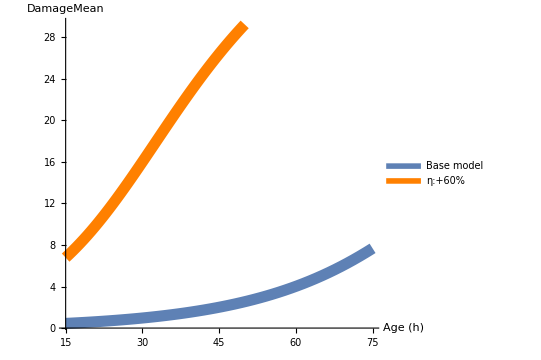
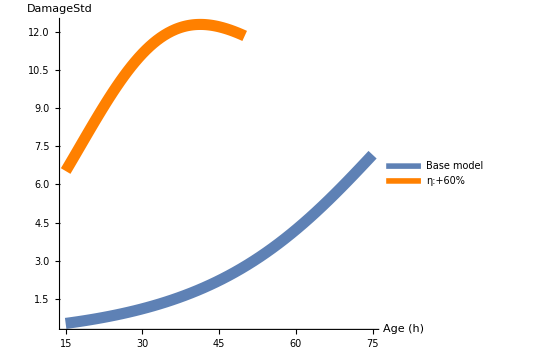
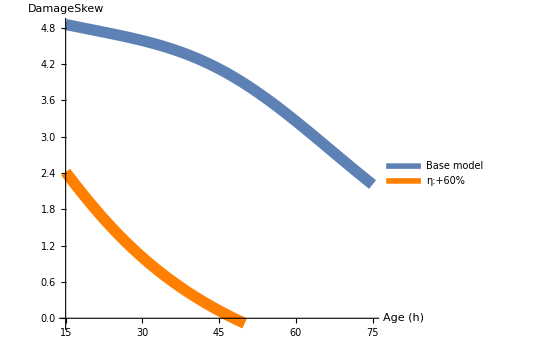
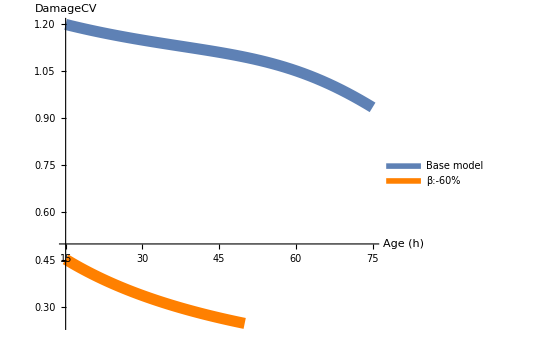
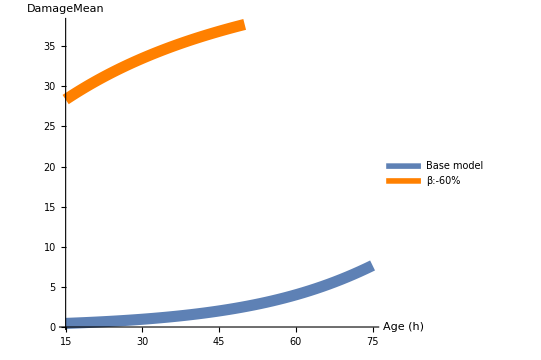
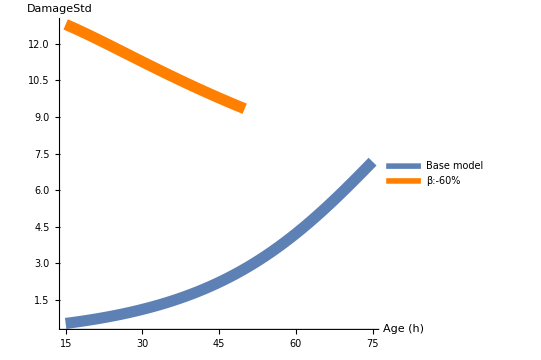
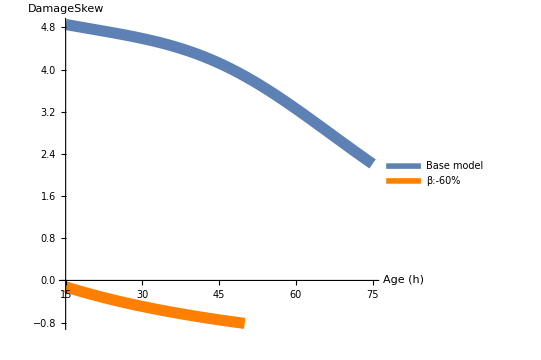
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[
Table[Table[Show[effect[[stat]],AxisLabel->{stat, "Age (h)"}, AspectRatio->.9],{stat,{"DamageCV","DamageMean","DamageStd","DamageSkew"}}],{effect,{momentsPlotsEta, momentsPlotsBeta,momentsPlotsKappa,momentsPlotsEps,momentsPlotsEtaBeta,momentsPlotsBetaEps}}],
Frame->All,ItemSize->{24,8}]
```

```mathematica
GraphicsGrid[Table[Table[Show[effect[[stat]],AxisLabel->{}, AspectRatio->.9],{stat,{"DamageCV","DamageMean","DamageStd","DamageSkew"}}],{effect,{momentsPlotsEta, momentsPlotsBeta,momentsPlotsKappa,momentsPlotsEps,momentsPlotsEtaBeta,momentsPlotsBetaEps}}],ImageSize->1000]
```

-Graphics-